```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY182_cloudy/sec_int_data/500nm.dat"]
```

{{1.83648,0.159479},{1.67469,0.230397},{1.55096,0.244827},{1.77833,0.196964},{1.08395,0.316124},{1.0884,1.76974},{1.10777,0.350516},{1.1184,0.370045},{1.90886,0.139066}}

1.52739-0.75825 x

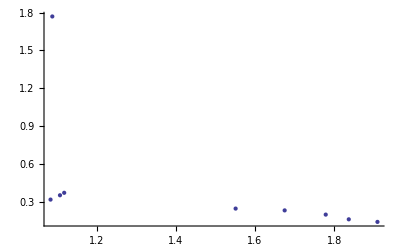

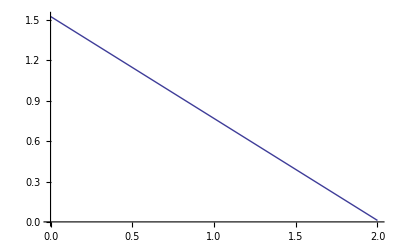

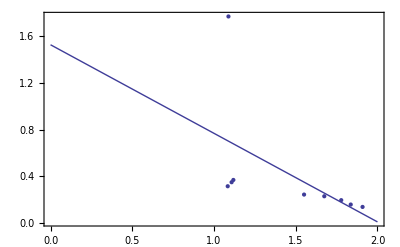

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```